In the limit ρ → 0 we assume ψ(i,a) = √(λ_(i',a'))ψ(i’,a’) where i’ and a’ are the renormalized indices afetr a decimation.

The goal of this Mathematica script is to test numerically whether such a scaling matrix λ_(i',a') exists, and to measure it.

```mathematica
(* Fibonacci Hamiltonian, in the co-basis, with periodic bc *)
hp[n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,1,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+Transpose[ar]]
]
```

```mathematica
(* periodic approximant of Fibonacci Hamiltonian, in the co-basis, k wavevector *)
h[k_,n_,tw_,ts_]:=Block[{F0=Fibonacci[n],F1=Fibonacci[n+1],F2=Fibonacci[n+2],tblw,tbls,ar},
tblw=Table[{i,i+F0}->tw,{i,2,F1}];
tbls=Table[{i,i+F1}->ts,{i,1,F0}];
PrependTo[tblw,{1,1+F0}->Exp[I k]tw];
ar=SparseArray[tblw,{F2,F2}]+SparseArray[tbls,{F2,F2}];
Normal[ar+ConjugateTranspose[ar]]
]
```

```mathematica
(* Intensity in the co-basis, ordered by IDoS label *)
Ik[k_,n_]:=Block[{val,vec,ts=10.,tw=1.},
{val,vec}=Eigensystem[h[k,n,tw,ts]];
(*order wavefunctions by increasing energy*)
Abs[vec[[Ordering[val]]]]^2
];
```

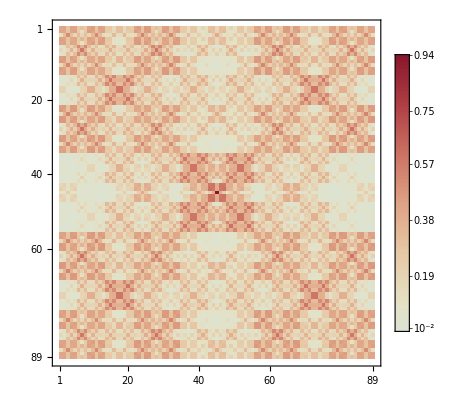

```mathematica
MatrixPlot[Ik[Pi/2,9],ColorFunction->"ThermometerColors",PlotLegends->Automatic]
```

```mathematica
n=9;
dk=0.05;
krange=Range[0,Pi,dk];
Iklist=ParallelMap[Ik[#,n]&,krange];
Imoy=Mean[Iklist];
```

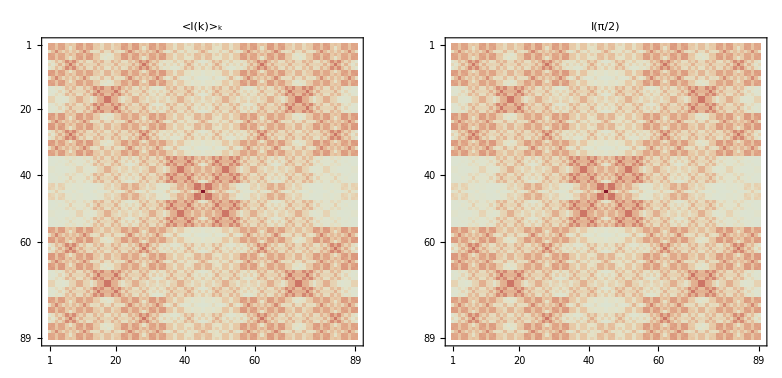

```mathematica
GraphicsRow[{MatrixPlot[Imoy,ColorFunction->"ThermometerColors",PlotLabel->"<I(k)>_k"],MatrixPlot[Ik[Pi/2,n],ColorFunction->"ThermometerColors",PlotLabel->"I(π/2)"]}]
```

When ρ → 0, we see that the intensity on each of the 4 squares of size F_(n-2)×F_(n-2) is the same (perhaps up to a reflection). So, indeed, the intensity on each one of the 4 squares write I(i,a) = λ_(i',a') I(i’,a’), where I(i’,a’) is the intensity at step n-2.

Measuring λ_(i',a')

Integrating intensity over the Brillouin zone

```mathematica
(* system size *)
n=9;
nd=n-2;
(* coupling *)
ρ=1./10;

dk=0.05;
krange=Range[0,Pi,dk];

(* intensity for the large system *)
Iklist=ParallelMap[Ik[#,n]&,krange];
i=Mean[Iklist];
(* intensity for the small (deflated) system *)
Iklist=ParallelMap[Ik[#,nd]&,krange];
id=Mean[Iklist];
```

```mathematica
(* crop the square [1,Subscript[F, n]]×[1,Subscript[F, n]] of the size Subscript[F, n+2] system *)
ic=i[[1;;Fibonacci[n],1;;Fibonacci[n]]];
```

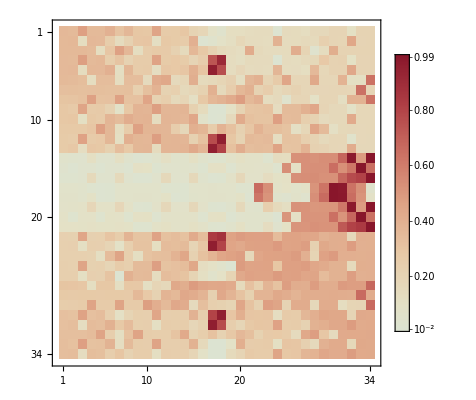

```mathematica
(* λ matrix *)
MatrixPlot[Abs[(2ic-id)/(2ic+id)],ColorFunction->"ThermometerColors",PlotLegends->Automatic]
```

Intensity for a fixed wavevector in the Brillouin zone

```mathematica
(* system size *)
n=9;
nd=n-2;
(* coupling *)
ρ=1./10;

k=Pi/2;

(* intensity for the large system *)
i=Ik[k,n];
(* intensity for the small (deflated) system *)
id=Ik[k,nd];
```

```mathematica
(* crop the square [1,Subscript[F, n]]×[1,Subscript[F, n]] of the size Subscript[F, n+2] system *)
ic=i[[1;;Fibonacci[n],1;;Fibonacci[n]]];
ic=i[[Fibonacci[n+1]+1;;Fibonacci[n+2],1;;Fibonacci[n]]];
ic=i[[1;;Fibonacci[n],Fibonacci[n+1]+1;;Fibonacci[n+2]]];
ic=i[[Fibonacci[n+1]+1;;Fibonacci[n+2],Fibonacci[n+1]+1;;Fibonacci[n+2]]];
```

Writing (I_c)_ij=(λ_ij(I_d))_ij, with λ_ij=1/2 + δλ_ij, we get
(2(I_c)_ij - (I_d)_ij)/(2(I_c)_ij + (I_d)_ij)=δλ_ij/(1+δλ_ij).

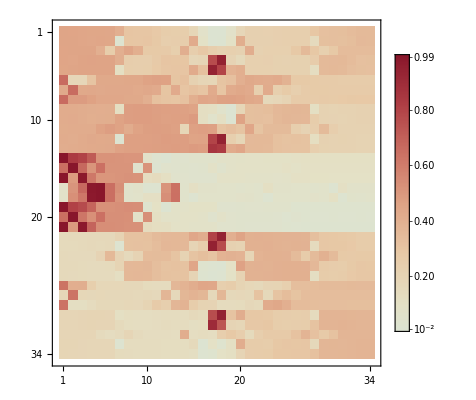

```mathematica
(* measuring δλ/(1+δλ) *)
MatrixPlot[Abs[(2ic-id)/(2ic+id)],ColorFunction->"ThermometerColors",PlotLegends->Automatic]
```

Measure λ only on the sites having nonzero amplitude in the ρ → 0 limit.

```mathematica
(* construct recursively a mask matrix: 1 for on sites having a nonzero amplitude in the ρ->0 limit, 0 elsewhere *)
recur[{m1_,m2_,m3_,n2_}]:=Block[{m},
(* create the new m2 array *)
m=ConstantArray[0,{Fibonacci[n2+2],Fibonacci[n2+2]}];

(* fill the 4 molecular clusters *)
m[[1;;Fibonacci[n2],1;;Fibonacci[n2]]]=m2;
m[[1;;Fibonacci[n2],Fibonacci[n2+1]+1;;Fibonacci[n2+2]]]=m2;
m[[Fibonacci[n2+1]+1;;Fibonacci[n2+2],1;;Fibonacci[n2]]]=m2;
m[[Fibonacci[n2+1]+1;;Fibonacci[n2+2],Fibonacci[n2+1]+1;;Fibonacci[n2+2]]]=m2;

(* fill the atomic cluster *)
m[[Fibonacci[n2]+1;;Fibonacci[n2+1],Fibonacci[n2]+1;;Fibonacci[n2+1]]]=m3;
{m,m1,m2,n2+1}]

(* initialization *)
m10={{1,1,0,1,1},{1,1,0,1,1},{0,0,1,0,0},{1,1,0,1,1},{1,1,0,1,1}};
m20={{1,0,1},{0,1,0},{1,0,1}};
m30={{1,1},{1,1}};
n0=4;

(* generate a mask of size Subscript[F, n+2]× Subscript[F, n+2] *)
genMask[n_]:=Nest[recur,{m10,m20,m30,n0},n-5][[1]];
```

```mathematica
(* large system size is Subscript[F, n+2] *)
n=9;
(* small system size is Subscript[F, nd+2] *)
nd=n-2;
(* fixed wavevector *)
k=Pi/2;
(* intensity for the large system *)
i=Ik[k,n];
(* intensity for the small (deflated) system *)
id=Ik[k,nd];
(* crop the square [1,Subscript[F, n]]×[1,Subscript[F, n]] of the size Subscript[F, n+2] system *)
ic1=i[[1;;Fibonacci[n],1;;Fibonacci[n]]];
ic2=i[[Fibonacci[n+1]+1;;Fibonacci[n+2],1;;Fibonacci[n]]];
ic3=i[[1;;Fibonacci[n],Fibonacci[n+1]+1;;Fibonacci[n+2]]];
ic4=i[[Fibonacci[n+1]+1;;Fibonacci[n+2],Fibonacci[n+1]+1;;Fibonacci[n+2]]];
icl={ic1,ic2,ic3,ic4};
```

```mathematica
(* λ matrix, having filtered to keep only sites having nonzero amplitude in the ρ = 0 limit *)
mask=genMask[n];
invMask=ConstantArray[1,{Fibonacci[n],Fibonacci[n]}]-mask;
filtIcL=(#*mask+0.5invMask)&/@icl;
filtId=id*mask+invMask;
```

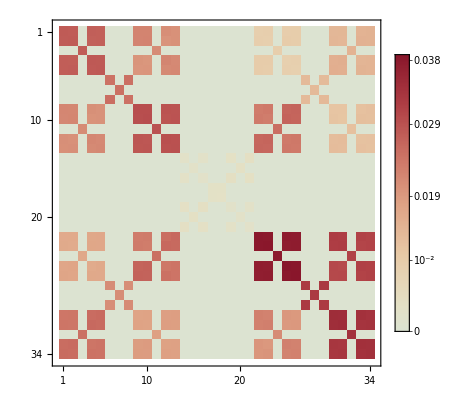

```mathematica
(* λ matrix *)
MatrixPlot[Abs[(2filtIcL[[1]]-filtId)/(2filtIcL[[1]]+filtId)],ColorFunction->"ThermometerColors",PlotLegends->Automatic]
```

```mathematica
Partition[{1,2,3,4},2]
```

{{1,2},{3,4}}

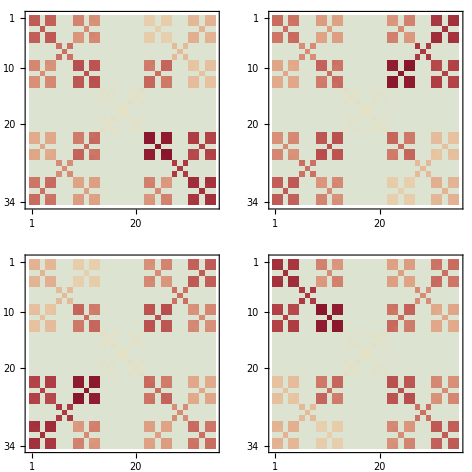

```mathematica
(* list of the 4 cropped matrices *)
listp=MatrixPlot[Abs[(2#-filtId)/(2#+filtId)],ColorFunction->"ThermometerColors"]&/@filtIcL;
(* reshape the list *)
listp=Partition[listp,2];
(* plot as a grid *)
GraphicsGrid[listp]
```

```mathematica
Integrate[1/(Sin[Pi u])^τ,{u,0,1}]
```

ConditionalExpression[Gamma[1/2-τ/2]/(√π Gamma[1-τ/2]),Re[τ]<1]

```mathematica
Gamma[1/2-τ/2]/(√π Gamma[1-τ/2])/.τ->-2
```

1/2

```mathematica
Integrate[1/(Sin[Pi u])^-4,{u,0,1}]
```

3/8

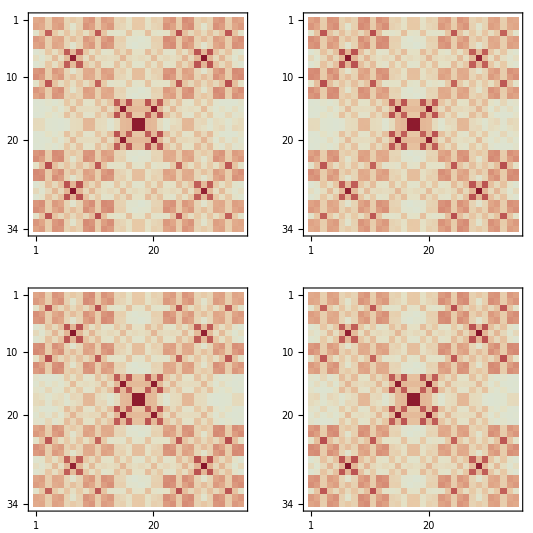

```mathematica
(* list of the 4 cropped matrices *)
listp=MatrixPlot[#,ColorFunction->"ThermometerColors"]&/@icl;
(* reshape the list *)
listp=Partition[listp,2];
(* plot as a grid *)
GraphicsGrid[listp]
```

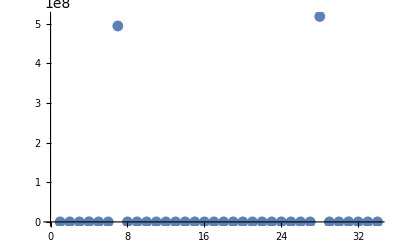

```mathematica
ListPlot[(Abs[wfcropped/wfd]^2)[[Fibonacci[n-3]-2]],PlotRange->All]
```